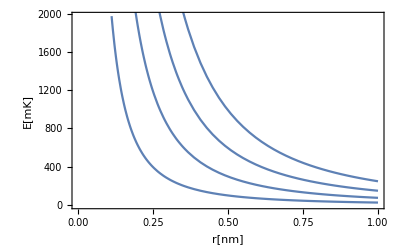

```mathematica
ℏ=1.0545718 10^-34;
amu=1.66054 10^-27;
mCs=133amu;
mNa=23amu;
nm=10^-9;
μK=10^-6;
mK=10^-3;
A=10^-10;
μ=(mNa mCs)/(mNa+mCs);
kB=1.38064852 10^-23;

Show[Plot[1/(kB mK)ℏ^2/(2μ)(#(#+1))/(r nm)^2,{r,0,1},Axes->False,Frame->True,FrameLabel->{"r[nm]","E[mK]"},LabelStyle->{Black,17}]&/@Range[1,4]]
```

for NaCs (http://iopscience.iop.org/article/10.1088/0953-4075/39/19/S08/pdf) a^3 Σ^+

```mathematica
C6
```

3.00609×10^-83

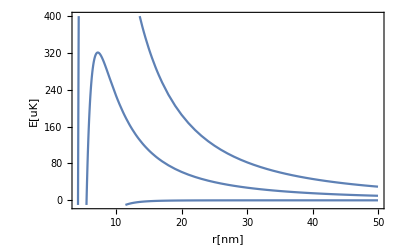

```mathematica
μ=(mNa mCs)/(mNa+mCs);
a0=0.53 10^-10;
C6=1.555214107 10^7 1.4 kB A^6;


Show[Plot[((ℏ^2# (#+1))/(2 μ (r nm)^2)-C6/(r nm)^6)/(kB uK),{r,1,50},PlotRange->{All,{-10,400}},Axes->False,Frame->True,FrameLabel->{"r[nm]","E[uK]"},LabelStyle->{Black,17}]&/@Range[0,2,1]]
```

for KRb

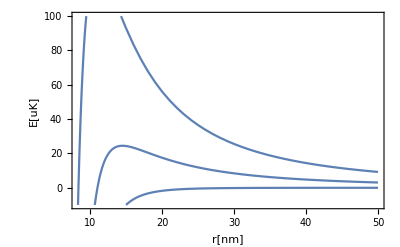

```mathematica
μ=(39+87)/2 amu;
a0=0.53 10^-10;
C6=16130 4.36 10^-18 a0^6;


Show[Plot[((ℏ^2# (#+1))/(2 μ (r nm)^2)-C6/(r nm)^6)/(kB uK),{r,1,50},PlotRange->{All,{-10,100}},Axes->False,Frame->True,FrameLabel->{"r[nm]","E[uK]"},LabelStyle->{Black,17}]&/@Range[0,2,1]]
```

```mathematica
GHz=10^9;
B=2π ℏ1GHz;
B J (J+1)/kB/.J->70
```

238.522